```mathematica
DSolve[y'[x]+x y[x] == x,y[x],x]
```

{{y[x]→1+ⅇ^(-x^2/2) C[1]}}

```mathematica
y[x_]:=1+ⅇ^(-x^2/2)
```

```mathematica
FullSimplify[D[y[x],x]]
```

-ⅇ^(-x^2/2) x

```mathematica
FullSimplify[D[y[x],{x,2}]]
```

ⅇ^(-x^2/2) (-1+x^2)

```mathematica
ya[x_]:=1+ⅇ^(-x^2/2)
```

```mathematica
dyadx[x_]:=-ⅇ^(-x^2/2) x
```

```mathematica
d2yadx2[x_]:=ⅇ^(-x^2/2)(x^2-1)
```

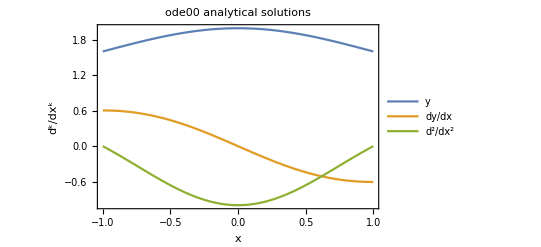

```mathematica
Plot[{ya[x],dyadx[x],d2yadx2[x]},{x,-1,1},FrameLabel->{{"d^k/dx^k",None},{"x",None}},PlotLegends->{"y","dy/dx","d^2/dx^2"},PlotLabel->"ode00 analytical solutions",
Frame->True]
```